# Pristanki meteoritov

## Analiza pristankov meteoritov

## Pridobitev podatkov

```mathematica
ResourceUpdate["Meteorite Landings"]
```

ResourceObject::newest: The most recent version of resource 11cdb199-4af7-49c3-b137-6f616722fcfc is already downloaded.

ResourceObject[…]

```mathematica
ResourceObject["Meteorite Landings"]
```

ResourceObject[…]

```mathematica
podatki=ResourceData["Meteorite Landings"]
```

Dataset[<>]

```mathematica
podatki[[1;;20]]
```

```mathematica
Tezki = podatki[Select[#Mass > Quantity[1000000, "Grams"]&]]
```

```mathematica
Tezki[1, "Coordinates"]
```

GeoPosition[{26.9667,-105.317}]

```mathematica
KoordinateTezki = Tezki[All, "Coordinates"]// Normal
```

{GeoPosition[{26.9667,-105.317}],GeoPosition[{44.05,126.167}],GeoPosition[{42.25,59.2}],GeoPosition[{39.6833,-99.8667}],GeoPosition[{46.16,134.653}],GeoPosition[{27.5,-12.5}],GeoPosition[{20.6,44.8833}],GeoPosition[{47.,88.}],GeoPosition[{26.2,-107.833}],GeoPosition[{-10.1167,-39.2}],GeoPosition[{49.9667,6.53333}],GeoPosition[{37.5825,-99.1636}],GeoPosition[{-14.258,-49.1592}],GeoPosition[{-27.4667,-60.5833}],GeoPosition[{35.05,-111.033}],GeoPosition[{76.1333,-64.9333}],GeoPosition[{30.4,-107.8}],GeoPosition[{23.0833,-101.017}],GeoPosition[{27.,-105.1}],GeoPosition[{28.7,-102.733}],GeoPosition[{-38.1,145.3}],GeoPosition[{44.4333,87.6333}],GeoPosition[{22.0183,26.0878}],GeoPosition[{19.2278,56.1428}],GeoPosition[{-25.5,18.}],GeoPosition[{41.98,-120.542}],GeoPosition[{-24.5667,133.167}],GeoPosition[{-19.5833,17.9167}],GeoPosition[{-22.3667,135.767}],GeoPosition[{-33.6167,24.}],GeoPosition[{-9.11667,33.0667}],GeoPosition[{27.05,-105.433}],GeoPosition[{-30.7833,127.55}],GeoPosition[{-29.5833,139.9}],GeoPosition[{25.1,107.7}],GeoPosition[{35.3333,-109.5}],Missing[NotAvailable],GeoPosition[{31.7167,-102.4}],GeoPosition[{34.4667,-115.233}],GeoPosition[{38.0833,-115.533}],GeoPosition[{19.2167,-98.3}],GeoPosition[{-26.2167,-48.6}],GeoPosition[{-16.2667,-47.95}],GeoPosition[{19.5667,-99.5667}],GeoPosition[{48.7,45.7}],GeoPosition[{-25.75,-70.5}],GeoPosition[{21.4997,50.4722}],GeoPosition[{45.3667,-122.583}],GeoPosition[{36.3,120.483}],GeoPosition[{24.2,113.4}],GeoPosition[{-32.1,117.717}],GeoPosition[{24.2333,111.183}]}

```mathematica
DrzavaPadca[Lokacija_]:=GeoNearest["Country", Lokacija, {All, Quantity[1, "Meters"]}]
```

```mathematica
DrzavaPadca[GeoPosition[{26.96667,-105.31667}]]
```

{Mexico}

```mathematica
PrestejPadce[Drzava_] :=Count[KoordinateTezki, x_/;(Head[x] =!=  Missing)  && GeoWithinQ[x, Drzava]]
```

```mathematica
PrestejPadce[Entity["Country", "Russia"]]
```

2

```mathematica
Drzave = {"Spain", "France", "Poland", "Russia", "China", "Brazil"}
```

{Spain,France,Poland,Russia,China,Brazil}

```mathematica
Table[{Drzave[[i]], PrestejPadce[Entity["Country", Drzave[[i]]]]},{ i, 1, Length[Drzave]}]//TableForm
```

Spain | 0
France | 0
Poland | 0
Russia | 2
China | 7
Brazil | 3

```mathematica
Letnice = podatki[All,"Year"]//Normal
```

{Year: 1880,Year: 1951,Year: 1952,Year: 1976,Year: 1902,Year: 1919,Year: 1949,Year: 1814,Year: 1930,Year: 1920,Year: 1974,Year: 1925,Year: 1769,Year: 1949,Year: 1838,Year: 1959,Year: 1981,Year: 1957,Year: 2001,Year: 1806,Year: 1766,Year: 1949,Year: 2002,Year: 1835,Year: 1873,Year: 1860,Year: 1900,Year: 1883,Year: 1899,Year: 1969,Year: 2008,45654,Year: 2006,Year: 1914,Year: 2011,Year: 2011,Year: 2011,Year: 1946,Year: 1792,Year: 1969,Year: 1919,Year: 1999,Year: 1987,Year: 1998,Year: 1998,Year: 1930,Year: 1984,Missing[NotAvailable],Year: 1998,Year: 2002,Year: 1955,Year: 1973,Year: 1967,Year: 1956,Year: 1983,Year: 1966,Year: 1981,Year: 1990,Year: 1990,Year: 1999,Year: 1939,Year: 2003,Year: 1976}
 |  |  |  |

```mathematica
Mase = podatki[All, "Mass"]// Normal
```

{21 g,720 g,107000 g,1914 g,780 g,4239 g,910 g,30000 g,1620 g,1440 g,1000 g,24000 g,Missing[NotAvailable],779 g,1800 g,3000 g,50000 g,160 g,700 g,6000 g,2000 g,625 g,252 g,700 g,3200 g,908 g,9251 g,228000 g,32000 g,2000000 g,3950 g,6000 g,6400 g,2700 g,3200 g,600 g,17900 g,256.8 g,Missing[NotAvailable],1500 g,6500 g,2500 g,320 g,15000 g,3200 g,810 g,5070 g,7450 g,41 g,9500 g,1300 g,2000 g,1280 g,94.2 g,265 g,1384.2 g,800 g,50000 g,2000 g,50000 g,9330 g,1230 g,146 g,134 g,2830 g,18000 g,10322 g,3700 g,345 g,1000 g,16700 g,11500 g,15000 g,14 g,629 g,6400 g,Missing[NotAvailable],3200 g,23.2 g,17 g,4500 g,44000 g,29560 g,15500 g,21000 g,86000 g,2900 g,1557 g,611 g,16000 g,14000 g,794 g,375 g,Missing[NotAvailable],3700 g,25000 g,19000 g,1770.5 g,3880 g,45000 g,2840 g,270 g,18000 g,1440 g,960 g,13.9 g,2000 g,1100 g,18 g,678 g,100 g,1047 g,2500 g,4000 g,1900 g,25000 g,488.1 g,560 g,6000 g,1039 g,1850 g,330000 g,705 g,2381 g,5100 g,470 g,67.8 g,7500 g,56 g,8800 g,256000 g,1676 g,8600 g,1342 g,7000 g,500 g,614 g,190 g,3599 g,5460 g,762 g,39000 g,1500 g,7250 g,219 g,303000 g,5300 g,2250 g,324 g,357 g,120000 g,1504 g,25000 g,5000 g,1500 g,29000 g,41000 g,25000 g,48500 g,212 g,478 g,2400 g,23680 g,4000 g,945 g,34000 g,1400 g,2300 g,750 g,342 g,8 g,7300 g,Missing[NotAvailable],94 g,15000 g,1360 g,1025 g,45.6 g,6460 g,3700 g,0.5 g,8200 g,18300 g,8800 g,1100 g,1810 g,31500 g,4300 g,27000 g,12000 g,4000 g,30000 g,2945 g,2936 g,100000 g,100000 g,6000 g,8400 g,705 g,1700 g,72 g,367 g,303 g,3920 g,Missing[NotAvailable],4000 g,1600 g,1455 g,48.6 g,104000 g,5200 g,469 g,5000 g,20350 g,1200 g,1460 g,78.4 g,3650 g,167 g,4255 g,17000 g,6000 g,18000 g,5650 g,1064 g,2000 g,100 g,7000 g,6580 g,340 g,28 g,0.8 g,16400 g,230 g,12500 g,25400 g,12000 g,1140 g,45000 g,1800 g,32000 g,3396 g,1000 g,400 g,166000 g,3950 g,10000 g,3840 g,1600 g,438 g,128800 g,230 g,5500 g,3891 g,1250 g,1161 g,642 g,5000 g,47700 g,1900 g,30 g,2270 g,Missing[NotAvailable],13200 g,577 g,2117 g,3230 g,300 g,188 g,10000 g,2400 g,3000 g,3336 g,840 g,10000 g,17226 g,5000 g,680.5 g,107000 g,54640 g,1470 g,127 g,8000 g,127000 g,277 g,113 g,107.2 g,20000 g,2250 g,1500 g,500 g,320000 g,89400 g,56000 g,1500 g,2360 g,380 g,3200 g,82 g,220 g,10200 g,17600 g,3640 g,152000 g,26000 g,6067 g,240 g,16300 g,Missing[NotAvailable],650 g,23000 g,11620 g,Missing[NotAvailable],4000 g,2500 g,132.7 g,36.1 g,28 g,5000 g,6400 g,Missing[NotAvailable],380 g,102 g,4162 g,Missing[NotAvailable],725 g,14290 g,18000 g,480 g,670 g,1303 g,152000 g,767 g,1750 g,1600 g,3618 g,9000 g,45.5 g,215 g,45038,301 g,64.2 g,18.92 g,4.23 g,5.99 g,6.86 g,7.86 g,79.02 g,68.24 g,20.38 g,13 g,13.91 g,15.51 g,3.57 g,20.69 g,7.77 g,18.98 g,5.74 g,6.57 g,355 g,176.7 g,18.99 g,11.54 g,6.97 g,7.31 g,7.73 g,9.15 g,7.91 g,6.7 g,7.49 g,7.43 g,6.28 g,5.93 g,5.93 g,4.92 g,4.74 g,6.52 g,4.93 g,4.6 g,4.65 g,5.92 g,4.32 g,5.24 g,4.98 g,3.76 g,3.97 g,4.7 g,3.18 g,3.13 g,3.26 g,4.83 g,17.36 g,52.91 g,17.89 g,13.74 g,15.1 g,14.65 g,11.7 g,12.81 g,9.96 g,8.7 g,7.56 g,6.25 g,7.22 g,3.06 g,3.79 g,4.04 g,5.53 g,3.41 g,81.56 g,55.79 g,50.58 g,42.9 g,29.95 g,31.47 g,29.84 g,16.69 g,20.28 g,57.03 g,41.15 g,19.04 g,15.54 g,12.16 g,10.39 g,12.5 g,9.22 g,8.56 g,44.17 g,33.75 g,18.3 g,4.2 g,32.16 g,29.86 g,70.64 g,6.01 g,4.25 g,7.44 g,6.73 g,8.14 g,97.09 g,18.44 g,139.3 g,5.67 g,7.25 g,3.87 g,4.27 g,16.32 g,4.52 g,29.37 g,4.07 g,81.77 g,7.17 g,4.53 g,34.61 g,12.84 g,5.25 g,3.6 g,3.41 g,81.5 g,5.72 g,5.81 g,38.95 g,8.1 g,289.71 g,27.39 g,25.8 g,7.01 g,10.79 g,10.26 g,154.9 g,522.4 g,199.2 g,21.76 g,15.3 g,7.22 g,20.16 g,133.5 g,42.11 g,107.6 g,27.69 g,15.98 g,295.7 g,632.7 g,10.7 g,7.76 g,7.7 g,6.59 g,4.54 g,4.5 g,101.1 g,18.87 g,8.12 g,9.84 g,7.05 g,295 g,162.4 g,19.76 g,20.65 g,8.48 g,46.38 g,4.47 g,11.93 g,3.89 g,7.94 g,3.35 g,4.65 g,21.87 g,7.02 g,184.3 g,14.24 g,7.1 g,6.75 g,4.25 g,94.74 g,40.36 g,27.71 g,75.73 g,16.81 g,15.11 g,194.5 g,77.31 g,60.53 g,22.42 g,13.7 g,17.21 g,8.02 g,7.48 g,9.18 g,6.19 g,4.98 g,3.48 g,35.09 g,82.19 g,6.67 g,6.33 g,5.93 g,21.23 g,6.09 g,12.36 g,8.82 g,6.95 g,12.36 g,41.23 g,9.48 g,41.29 g,15.99 g,4.69 g,49.16 g,3.56 g,6.56 g,10.06 g,13.93 g,12.342 g,54.92 g,16.66 g,12.08 g,8.1 g,24.89 g,13.65 g,10.07 g,39.17 g,7.36 g,9.03 g,21.69 g,62.16 g,15.21 g,3.17 g,19.28 g,14.22 g,5.3 g,216.2 g,126.5 g,49.89 g,22.96 g,21.56 g,6.82 g,3.34 g,62.66 g,12.89 g,4.95 g,7.02 g,57.4 g,5.05 g,6.8 g,10.34 g,9.83 g,53.05 g,7.91 g,3.32 g,10.18 g,82.55 g,38.67 g,3.94 g,7.89 g,15.42 g,26.96 g,3.11 g,6.81 g,5.05 g,7.2 g,6.92 g,11.72 g,11.92 g,3.72 g,6.06 g,3.64 g,8.85 g,18.16 g,36.17 g,3.42 g,8.23 g,11.38 g,8.89 g,47.67 g,28.74 g,11.47 g,15.72 g,5.45 g,37.44 g,54.8 g,19.32 g,118.9 g,4.59 g,3.2 g,5800 g,421000 g,3290 g,5750 g,913 g,500 g,14 g,4.6 g,1500 g,9600 g,262.5 g,15000 g,4.5 g,76000 g,132000 g,40000 g,3000000 g,5920 g,60000 g,835 g,1440 g,3500 g,118400 g,3800000 g,218000 g,140700 g,3 g,25.9 g,200 g,7600 g,1000000 g,6660 g,3000 g,300 g,50000 g,8680 g,85000 g,Missing[NotAvailable],27.7 g,162000 g,6700 g,1058 g,3700 g,76 g,630000 g,16000 g,2000000 g,900000 g,100000 g,1475 g,172 g,46 g,3.3 g,2167 g,200 g}
 |  |  |  |

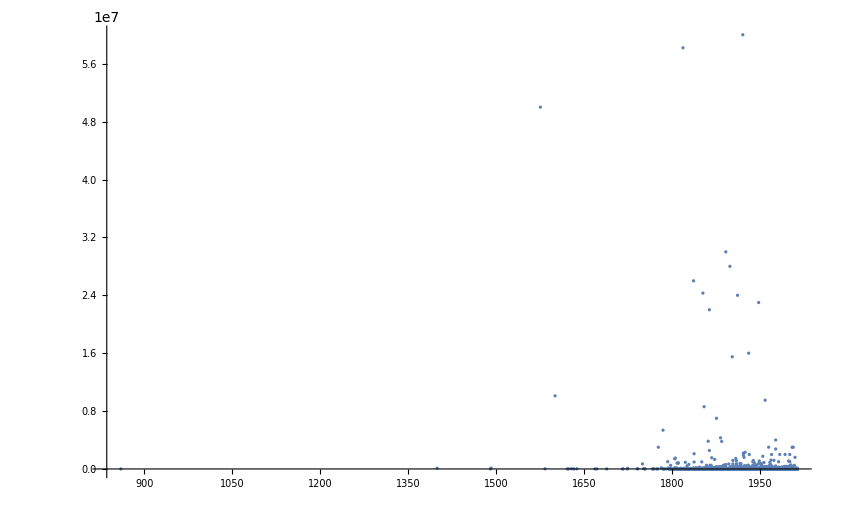

```mathematica
ListPlot[Table[{DateValue[Letnice[[i]], "Year"], QuantityMagnitude[Mase[[i]]]},{i, 1, Length[Mase]}], PlotRange->All]
```

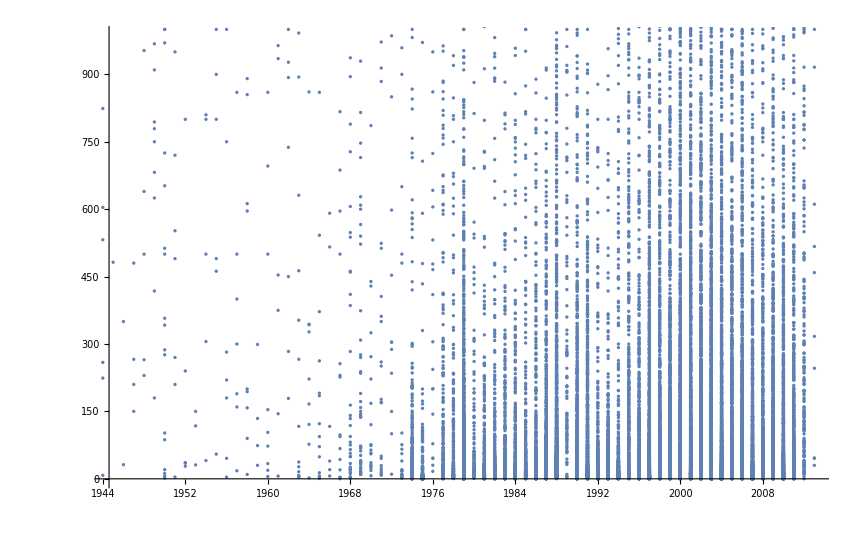

```mathematica
ListPlot[Table[{DateValue[Letnice[[i]], "Year"], QuantityMagnitude[Mase[[i]]]},{i, 1, Length[Mase]}]]
```

```mathematica
QuantityMagnitude[Mase[[1]]]
```

21

```mathematica
QuantityMagnitude[Letnice[[1]]]
```

QuantityMagnitude[Year: 1880]

```mathematica
FullForm[Letnice[[1]]]
```

DateObject[List[1880],"Year","Gregorian",-5.]

```mathematica
DateValue[Letnice[[1]], "Year"]
```

1880

## Prikazovanje področiji padlih meteoritov

```mathematica
GeoGraphics[{Red,PointSize[0.09],Opacity[0.2],Point@DeleteMissing[ResourceData["Meteorite Landings"][All,"Coordinates"]]},GeoRange->Entity["Country","Slovenia"],ImageSize->600]
```

-Graphics-

Nenatančni pristanki treh meteoritov v Sloveniji (in trije na Hrvaškem).

```mathematica
GeoGraphics[{Red,PointSize[0.007],Opacity[0.7],Point@DeleteMissing[ResourceData["Meteorite Landings"][All,"Coordinates"]]},GeoRange->Entity["Country","Slovenia"],ImageSize->800]
```

-Graphics-

Natančnejši pristanki meteoritov v Sloveniji .

Kot je na sliki razvidno so vsi trije meteoriti padli v vzhodni Sloveniji.

## Primerjava padlih meteoritov s Portugalsko in Ekvadorjem

```mathematica
GeoGraphics[{Red,PointSize[0.04],Opacity[0.7],Point@DeleteMissing[ResourceData["Meteorite Landings"][All,"Coordinates"]]},GeoRange->Entity["Country","Portugal"],ImageSize->600]
```

-Graphics-

Na portugalskem je bilo zabeleženih še enkrat toliko mateoritov kakor na slovenskem, torej 6.

```mathematica
GeoGraphics[{Red,PointSize[0.04],Opacity[0.7],Point@DeleteMissing[ResourceData["Meteorite Landings"][All,"Coordinates"]]},GeoRange->Entity["Country","Ecuador"],ImageSize->600]
```

-Graphics-

V Ekvadorju pa je bila ena tretina tega kar je bilo zabeleženo v Sloveniji, torej eden .

WolframAlphaQueryParseResults

20273. km^2

WolframAlphaQueryParseResults

92090. km^2

WolframAlphaQueryParseResults

283561. km^2

```mathematica
Ratios[3/20273,1/283561,6/92090]
```

Ratios::listrp: List or SparseArray or structured array expected at position 1 in Ratios[3/20273,1/283561,3/46045].

Ratios[3/20273,1/283561,3/46045]

Kot lahko vidimo iz izračuna so padli meteoriti najpogostejši v Sloveniji glede na površino vsake izmed treh držav.